```mathematica
(*These results are for Imχ*)
Ω=ω+ⅈ*Γ;
A=-(Ω)^2+1+δ^2;
B=2*1*δ;
Λ=-2(δ^2/(A √(1-(B/A)^2))-(A/(4*δ^2)-1)(1-1/(√(1-(B/A)^2))));(*Subscript[π, 22]*)
Ξ=-2(1+Ω^2/(A √(1-(B/A)^2)));(*Subscript[π, 33]*)
Φ=(ⅈ*Ω)/δ(1+(2*δ^2-A)/(A √(1-(B/A)^2)));(*Subscript[π, 23]*)
Ψ=-(ⅈ*Ω)/δ(1+(2*δ^2-A)/(A √(1-(B/A)^2)));(*Subscript[π, 32]*)
ψ=-2((A-A √(1-(B/A)^2))/(2δ)^2); (*Subscript[π, 11]*)
f1[α_]:=1+u/2(Λ+Ξ+u/2(Λ*Ξ-Φ*Ψ))(*Mode equation arising from Subscript[π, 22],Subscript[π, 33],Subscript[π, 23],Subscript[π, 32] *)
h[α_]:=1+u/2 ψ;
χ1=-Im[(ω*ψ)/(h[α]+ⅈ*σ)];
χ2=-Im[(ω(Λ(1+u/2 Ξ)-u/2 Φ*Ψ))/(f1[α]+ⅈ*σ)];
χ3=-Im[(ω(Ξ(1+u/2 Λ)-u/2 Φ*Ψ))/(f1[α]+ⅈ*σ)];
χ4=Im[(ω*Φ)/(f1[α]+ⅈ*σ)];
χ5=Im[(ω*Ψ)/(f1[α]+ⅈ*σ)];(*χ5=χ4*)
```

```mathematica
Δ=1;(*Rashba Spin Orbit Coupling*)
u=.3;(*Coulomb energy time density of states*)
Γ=.05;
σ=0.0;
α=4;
δ=(α/Δ)/(1-u);(*Renormalized zeeman energy. Here α is α/Subscript[ϵ, F]*)
A1=Abs[1-δ/Δ];
A2=Abs[1+δ/Δ];
```

```mathematica
ρ=χ2;
S1=ListLinePlot[Table[ {ω,ρ},{ω,2,7,0.05}],PlotRange->Full,PlotStyle->{Black,Thickness[.003]}];
```

```mathematica
Δ=1;(*Rashba Spin Orbit Coupling*)
u=.19;(*Coulomb energy time density of states*)
Γ=.05;
σ=0.0;
α=4;
δ=(α/Δ)/(1-u);(*Renormalized zeeman energy. Here α is α/Subscript[ϵ, F]*)
A3=Abs[1-δ/Δ];
A4=Abs[1+δ/Δ];
```

```mathematica
ρ=χ2;
S2=ListLinePlot[Table[ {ω,ρ},{ω,2,7,0.05}],PlotRange->Full,PlotStyle->{Green,Thickness[.003]}];
```

```mathematica
Δ=1;(*Rashba Spin Orbit Coupling*)
u=.1;(*Coulomb energy time density of states*)
Γ=.05;
σ=0.0;
α=4;
δ=(α/Δ)/(1-u);(*Renormalized zeeman energy. Here α is α/Subscript[ϵ, F]*)
A5=Abs[1-δ/Δ];
A6=Abs[1+δ/Δ];
```

```mathematica
ρ=χ2;
S3=ListLinePlot[Table[ {ω,ρ},{ω,2,7,0.05}],PlotRange->Full,PlotStyle->{Red,Thickness[.003]}];
```

```mathematica
Δ=1;(*Rashba Spin Orbit Coupling*)
u=.0;(*Coulomb energy time density of states*)
Γ=.05;
σ=0.0;
α=4;
δ=(α/Δ)/(1-u);(*Renormalized zeeman energy. Here α is α/Subscript[ϵ, F]*)
A7=Abs[1-δ/Δ];
A8=Abs[1+δ/Δ];
```

```mathematica
ρ=χ2;
S4=ListLinePlot[Table[ {ω,ρ},{ω,2,7,0.05}],PlotRange->Full,PlotStyle->{Blue,Thickness[.003]}];
```

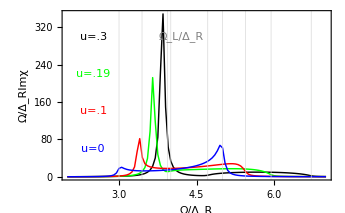

```mathematica
Show[{S1,S2,S3,S4},Frame->True,FrameLabel->{" Ω/Δ_R"," Ω/Δ_RImχ "},GridLines->{{{α,{Gray,Thickness[0.003],Dashed}},{A1,{Black,Thickness[0.003]}},{A2,{Black,Thickness[0.003]}},{A3,{Green,Thickness[0.003]}},{A4,{Green,Thickness[0.003]}},{A5,{Red,Thickness[0.003]}},{A6,{Red,Thickness[0.003]}},{A7,{Blue,Thickness[0.003]}},{A8,{Blue,Thickness[0.003]}}},None},BaseStyle->{FontFamily->"Arial",10,SingleLetterItalics->True},Epilog->{Thickness[0.5],Black,Text[" u=.3",{2.5,300}],Thickness[.5],Green,Text[" u=.19",{2.5,220}],Thickness[0.5],Red,Text[" u=.1",{2.5,140}],Thickness[0.5],Blue,Text[" u=0",{2.5,60}],Thickness[0.5],Gray,Text[" Ω_L/Δ_R",{4.2,300}]}]
```